## 导入数据

```mathematica
SetDirectory["C:\\Users\\Rick\\Desktop\\FundModel\\DFFC-FundModel\\csv_data"];
data10=Reverse[Drop[Import["010365.csv"],1]ᵀ[[4]]ᵀ];
data1=Table[{i,data10[[i]]},{i,-Length[data10],-1}];
datadate1=Drop[Import["010365.csv"],1]ᵀ[[2]];
data20=Reverse[Drop[Import["001595.csv"],1]ᵀ[[4]]ᵀ];
data2=Table[{i,data20[[i]]},{i,-Length[data20],-1}];
datadate2=Drop[Import["001595.csv"],1]ᵀ[[2]];
```

```mathematica
SlidingAverage[arr_,window_Integer]:=Module[{n,half},
n=Length[arr];
half=Floor[window/2];
Table[With[{start=Max[1,i-half],end=Min[n,i+half]},Mean[arr[[start;;end]]]],{i,1,n}]]
```

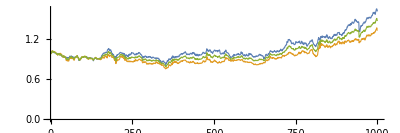

```mathematica
start=1000;
d1=data1ᵀ[[2]][[-start;;-1]];
d2=data2ᵀ[[2]][[-start;;-1]];
d1=d1/d1[[1]];
d2=d2/d2[[1]];
ListLinePlot[{d1,d2,(d1+d2)/2},PlotLegends->{中证红利,南方,混合},PlotStyle->Thickness[0.002],AspectRatio->1/3]
```

```mathematica
@
```

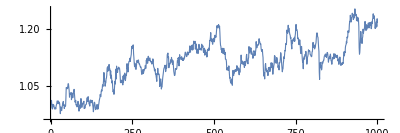

```mathematica
ListLinePlot[d1/d2,PlotStyle->Thickness[0.002],AspectRatio->1/3]
```

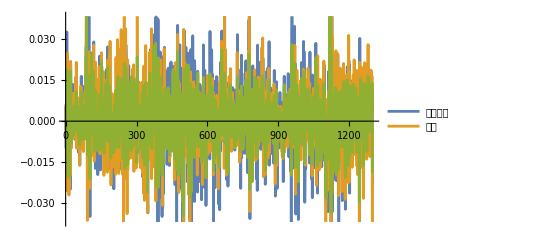

```mathematica
ListLinePlot[Differences/@{d1,d2,d1/2+d2/2},PlotLegends->{中证红利,南方}]
```

```mathematica
StandardDeviation/@{d1,1.141d2,d1(1/(1+1.141))+d2(1.141/(1+1.141))}
```

{0.244262,0.244279,0.227038}